```mathematica
ClearAll["Global`*"]
```

```mathematica
Dd[n_,0,a_]:=1;Dd[n_,1,a_]:=Floor[n]-a+1
Dd[n_,k_,a_]:=Dd[n,k,a]=Sum[Binomial[k,j] Dd[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
P2[n_,k_]:=P2[n,k]=Sum[FullSimplify[MangoldtLambda[j]/Log[j]] P2[n/j,k-1],{j,2,Floor[n]}];P2[n_,0]:=1
P1[x_,z_]:=Sum[bin[z,k] P2[x,k],{k,0,Log[2,x]}]
PP2[n_, k_] := D[P1[n,z],{z,k}]/.z->0
P2Alt[n_,j_]:=Sum[1/k!(D[Log[1+x]^j,{x,k}]/.x->0) Dd[n,k,2],{k,0,Log[2,n]}]
PP2Alt[n_,j_]:=Sum[1/k!(D[Log[1+Log[1+x]]^j,{x,k}]/.x->0) Dd[n,k,2],{k,0,Log[2,n]}]
PP3Alt[n_,j_]:=Sum[1/k!(D[Log[1+Log[1+Log[1+x]]]^j,{x,k}]/.x->0) Dd[n,k,2],{k,0,Log[2,n]}]
PP4Alt[n_,j_]:=Sum[1/k!(D[Log[1+Log[1+Log[1+Log[1+x]]]]^j,{x,k}]/.x->0) Dd[n,k,2],{k,0,Log[2,n]}]
PP5Alt[n_,j_]:=Sum[1/k!(D[Log[1+Log[1+Log[1+Log[1+Log[1+x]]]]]^j,{x,k}]/.x->0) Dd[n,k,2],{k,0,Log[2,n]}]
```

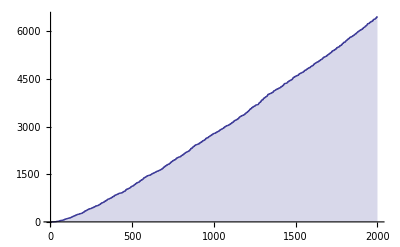

```mathematica
DiscretePlot[ P2Alt[n,4],{n,1,2000}]
```

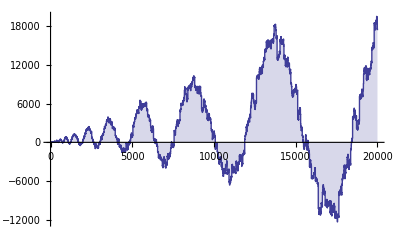

```mathematica
DiscretePlot[ PP2Alt[n,4],{n,1,20000}]
```

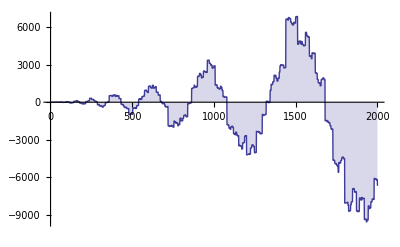

```mathematica
DiscretePlot[ PP3Alt[n,4],{n,1,2000}]
```

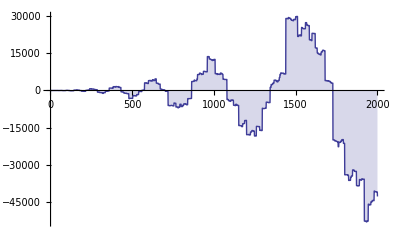

```mathematica
DiscretePlot[ PP4Alt[n,4],{n,1,2000}]
```

```mathematica
DiscretePlot[ PP5Alt[n,4],{n,1,2000}]
```

$Aborted

```mathematica
Limit[ D[ x/Log[1+x],{x,4}],x->0]
```

-19/30